### Auxiliary Functions

```mathematica
insideQ[{p1_,p2_,p3_},v_]:=(Det[{v,p3-p1}]-Det[{p1,p3-p1}])/Det[{p2-p1,p3-p1}]>0&&(Det[{p1,p2-p1}]-Det[{v,p2-p1}])/Det[{p2-p1,p3-p1}]>0&&(Det[{v,p3-p1}]-Det[{p1,p3-p1}]+Det[{p1,p2-p1}]-Det[{v,p2-p1}])/Det[{p2-p1,p3-p1}]<1
findTriangle[pts_]:=Module[{xmin,xmax,ymin,ymax,cpts},
cpts=pts;
{{xmin,xmax},{ymin,ymax}}=MinMax/@Transpose[cpts];
{Abs[1/2 (-p1y p2x+p1x p2y+p1y p3x-p2y p3x-p1x p3y+p2x p3y)],{{p1x,p1y},{p2x,p2y},{p3x,p3y}}}/.FindMinimum[{ 
(-p1y p2x+p1x p2y+p1y p3x-p2y p3x-p1x p3y+p2x p3y)^2,
(And@@(insideQ[{{p1x,p1y},{p2x,p2y},{p3x,p3y}},#]&/@cpts))},
{{p1x,xmin},{p1y,ymin},{p2x,xmax+ymax},{p2y,ymin},{p3x,xmin},{p3y,xmax+ymax}}][[2]]]
MyCurvePath[x_]:=Module[{a=Mean[x]},Append[#,#[[1]]]&@SortBy[x,ArcTan@@(#-a)&]]
```

### Sun and Zhang, 2020 “ethnic group” simulation

```mathematica
SZdata=Import["/Users/avimayo/Downloads/Default Dataset.csv"];
SZcdata=FindClusters[data,3];
```

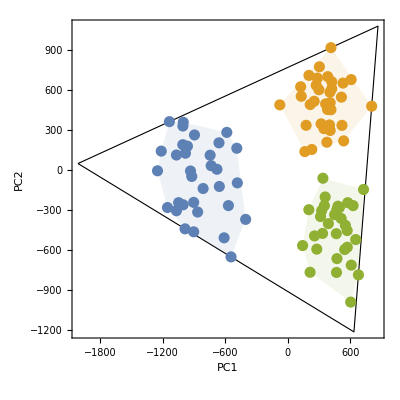

```mathematica
SZTriangle=findTriangle[MeshCoordinates@ConvexHullMesh@SZdata][[2]];
Show[{Graphics[{FaceForm[],EdgeForm[Black],Triangle@SZTriangle}],Graphics[Thread[{ColorData[97]/@{1,2,3},Opacity[.1],Polygon/@MyCurvePath/@Chop/@MeshCoordinates/@ConvexHullMesh/@SZcdata}]],ListPlot[cdata,PlotStyle->PointSize[.02]]},Frame->True,AspectRatio->1,FrameLabel->{"PC1","PC2"}]
```

SibSwapped data is enclosed by practically the same triangle since shuffling within a cluster hardly change the distribution of points.

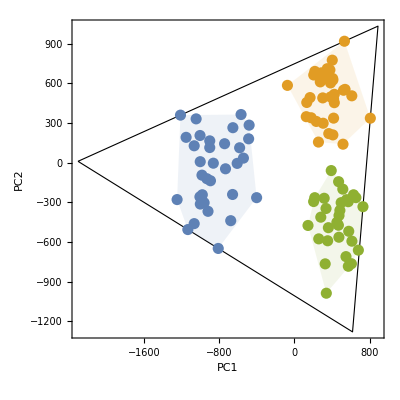

```mathematica
RandomSZcdata=({#[[;;,1]],RandomSample@#[[;;,2]]}ᵀ&/@SZcdata);
RandomSZTriangle=findTriangle[MeshCoordinates@ConvexHullMesh@(Join@@RandomSZcdata)][[2]];
Show[{
Graphics[{FaceForm[],EdgeForm[Black],Triangle@RandomSZTriangle}],
Graphics[Thread[{ColorData[97]/@{1,2,3},Opacity[.1],Polygon/@MyCurvePath/@Chop/@MeshCoordinates/@ConvexHullMesh/@RandomSZcdata}]],
ListPlot[RandomSZcdata,PlotStyle->PointSize[.02]]},Frame->True,AspectRatio->1,FrameLabel->{"PC1","PC2"}]
```

```mathematica
SZRealTRatio=Abs[1-(findTriangle[MeshCoordinates@#][[1]])/(RegionMeasure@#)]&@ConvexHullMesh@SZdata
```

0.209139

```mathematica
SZrandomdata=Table[Abs[1-(findTriangle[MeshCoordinates@#][[1]])/(RegionMeasure@#)]&@ConvexHullMesh@(Join@@({#[[;;,1]],RandomSample@#[[;;,2]]}ᵀ&/@SZcdata)),10^3];
```

```mathematica
N@(LengthWhile[Sort[#],#<=SZRealTRatio&]/(Length@#))&@Select[SZrandomdata,#<.5&]
```

0.0967033

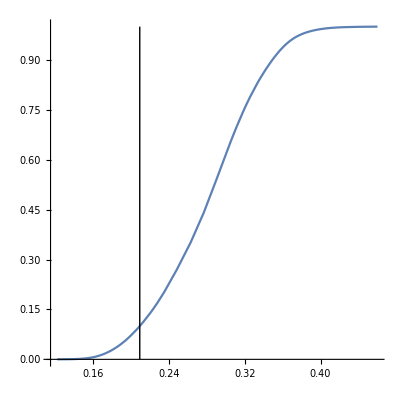

```mathematica
SmoothHistogram[Select[SZrandomdata,#<.5&],Automatic,"CDF",AspectRatio->1,Epilog->Line[{{SZRealTRatio,0},{SZRealTRatio,1}}]]
```

### Cancer data (Hausser et.al 2019)

```mathematica
cancerdata=Import["/Users/avimayo/Downloads/visAnc.csv"];
```

```mathematica
GatherBy[cancerdata[[2;;]],Last][[;;,1,-1]]
```

{european,african,other,east asian}

```mathematica
Length/@GatherBy[cancerdata[[2;;]],Last][[;;,;;,;;2]]
```

{449,15,22,10}

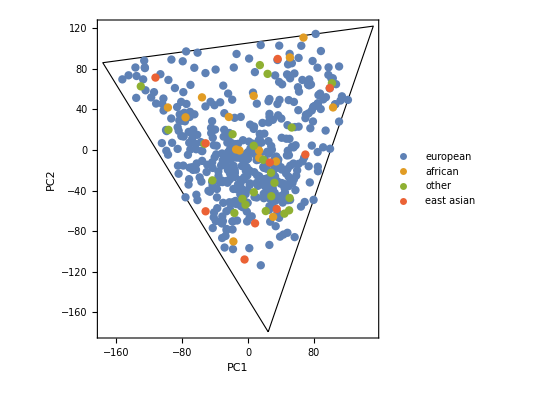

```mathematica
cancertri=findTriangle[MeshCoordinates@ConvexHullMesh@(cancerdata[[2;;,;;2]])][[2]];
Show[{
Graphics[{FaceForm[],EdgeForm[Black],Triangle@cancertri}],
ListPlot[GatherBy[cancerdata[[2;;]],Last][[;;,;;,;;2]],PlotStyle->PointSize[.015],PlotLegends->Placed[{"european","african","other","east asian"},Scaled@{.2,.2}]]},Frame->True,AspectRatio->1,FrameLabel->{"PC1","PC2"}]
```

```mathematica
CancerTratioDist=ParallelMap[(Abs[1-(RegionMeasure@#)/(findTriangle[MeshCoordinates@#][[1]])]&@ConvexHullMesh@#)&,(Join@@@((Table[RandomSample[#,10],10^3]&/@GatherBy[cancerdata[[2;;]],Last][[;;,;;,;;2]])ᵀ))];
```

```mathematica
CancerRandomTratioDist=ParallelMap[(Abs[1-(RegionMeasure@#)/(findTriangle[MeshCoordinates@#][[1]])]&@ConvexHullMesh@#)&,(Join@@@((Table[{#[[;;,1]],RandomSample[#[[;;,2]]]}ᵀ&@RandomSample[#,10],10^3]&/@GatherBy[cancerdata[[2;;]],Last][[;;,;;,;;2]])ᵀ))];
```

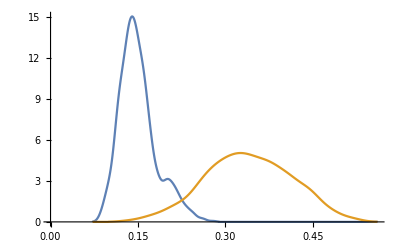

```mathematica
SmoothHistogram[{CancerTratioDist,CancerRandomTratioDist}]
```

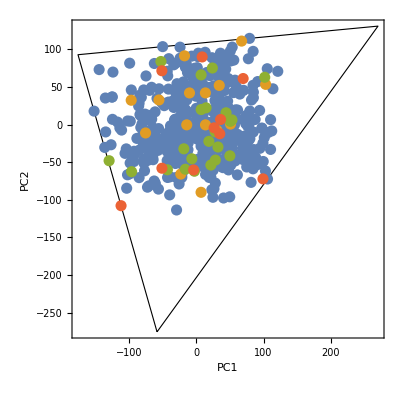

```mathematica
RandomCancerData=({#[[;;,1]],RandomSample@#[[;;,2]]}ᵀ&/@(GatherBy[cancerdata[[2;;]],Last][[;;,;;,;;2]]));
RandomCancerTriangle=findTriangle[MeshCoordinates@ConvexHullMesh@(Join@@RandomCancerData)][[2]];
Show[{
Graphics[{FaceForm[],EdgeForm[Black],Triangle@RandomCancerTriangle}],
ListPlot[RandomCancerData,PlotStyle->PointSize[.02]]},Frame->True,AspectRatio->1,FrameLabel->{"PC1","PC2"}]
```

#### Downsampling the groups

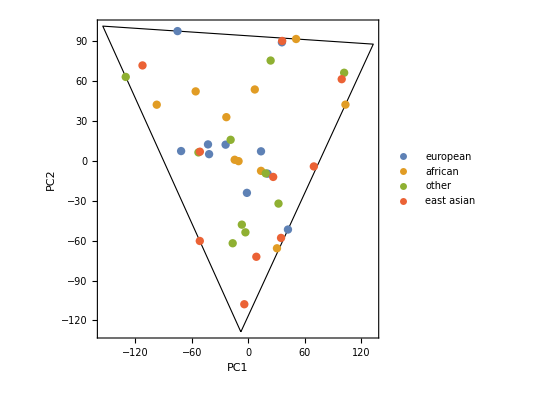

```mathematica
DScancerdata=((Join@@(RandomSample[#,Min[{10,Length@#}]]&/@GatherBy[cancerdata[[2;;]],Last][[;;,;;,;;2]])));
DSCancerTriangle=findTriangle[MeshCoordinates@ConvexHullMesh@DScancerdata][[2]];
Show[{
Graphics[{FaceForm[],EdgeForm[Black],Triangle@DSCancerTriangle}],
ListPlot[Partition[DScancerdata,10],PlotStyle->PointSize[.015],PlotLegends->Placed[{"european","african","other","east asian"},Scaled@{.2,.2}]]},Frame->True,AspectRatio->1,FrameLabel->{"PC1","PC2"}]
```

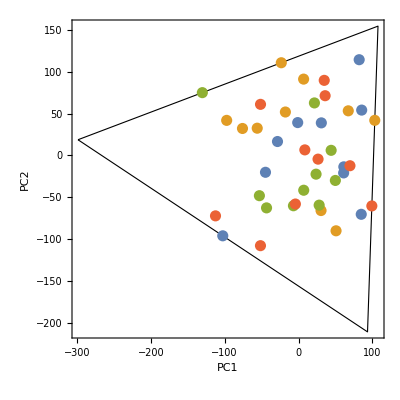

```mathematica
randomdata=({#[[;;,1]],RandomSample@#[[;;,2]]}ᵀ&/@(RandomSample[#,Min[{10,Length@#}]]&/@GatherBy[cancerdata[[2;;]],Last][[;;,;;,;;2]]));
RandomTriangle=findTriangle[MeshCoordinates@ConvexHullMesh@(Join@@randomdata)][[2]];
Show[{
Graphics[{FaceForm[],EdgeForm[Black],Triangle@RandomTriangle}],
ListPlot[randomdata,PlotStyle->PointSize[.02]]},Frame->True,AspectRatio->1,FrameLabel->{"PC1","PC2"}]
```

```mathematica
CancerTRatio=Abs[1-(findTriangle[MeshCoordinates@#][[1]])/(RegionMeasure@#)]&@ConvexHullMesh@cancerdata[[2;;,;;2]]
```

0.186672

```mathematica
GatheredCancerData=GatherBy[cancerdata[[2;;]],Last][[;;,;;,;;2]];
```

```mathematica
Cancerrandomdata=ParallelTable[Abs[1-(findTriangle[MeshCoordinates@#][[1]])/(RegionMeasure@#)]&@ConvexHullMesh@(Join@@({#[[;;,1]],RandomSample@#[[;;,2]]}ᵀ&/@GatheredCancerData)),10^3];
```

```mathematica
N@(LengthWhile[Sort[#],#<=CancerTRatio&]/(Length@#))&@Select[Cancerrandomdata,#<.5&]
```

0.

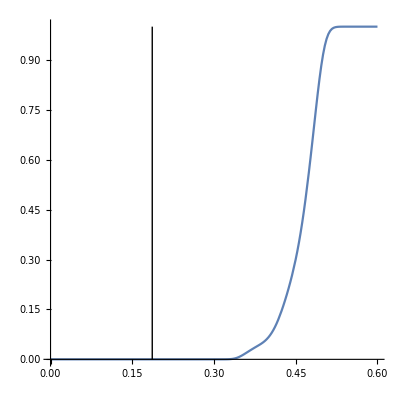

```mathematica
SmoothHistogram[Select[Cancerrandomdata,#<.5&],Automatic,"CDF",AspectRatio->1,Epilog->Line[{{CancerTRatio,0},{CancerTRatio,1}}],PlotRange->{{0,.6},{0,1}}]
```

#### Gaussian Mixture model of the cancer data gives poor p-value

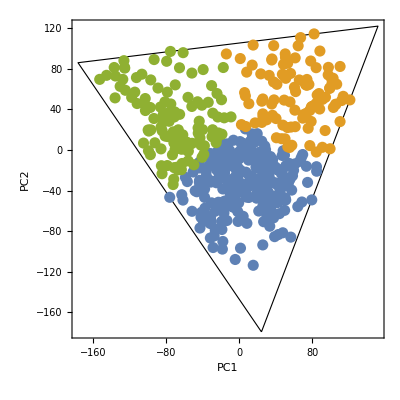

```mathematica
GMdata=FindClusters[cancerdata[[2;;,;;2]],Method->"GaussianMixture"];
GMtri=findTriangle[MeshCoordinates@ConvexHullMesh@(Join@@GMdata)][[2]];
Show[{
Graphics[{FaceForm[],EdgeForm[Black],Triangle@GMtri}],
ListPlot[GMdata,PlotStyle->PointSize[.02]]},Frame->True,AspectRatio->1,FrameLabel->{"PC1","PC2"}]
```

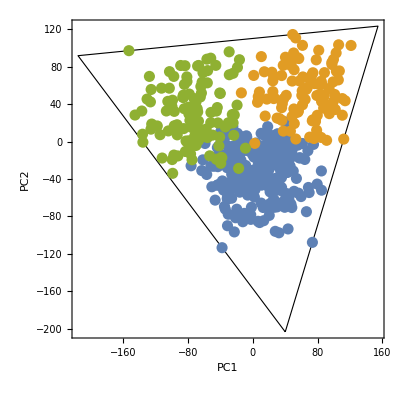

```mathematica
RandomGMdata={#[[;;,1]],RandomSample@#[[;;,2]]}ᵀ&/@GMdata;
RandomGMtri=findTriangle[MeshCoordinates@ConvexHullMesh@(Join@@RandomGMdata)][[2]];
Show[{
Graphics[{FaceForm[],EdgeForm[Black],Triangle@RandomGMtri}],
ListPlot[RandomGMdata,PlotStyle->PointSize[.02]]},Frame->True,AspectRatio->1,FrameLabel->{"PC1","PC2"}]
```

```mathematica
clusteredCancerrandomdata=ParallelTable[Abs[1-(findTriangle[MeshCoordinates@#][[1]])/(RegionMeasure@#)]&@ConvexHullMesh@(Join@@({#[[;;,1]],RandomSample@#[[;;,2]]}ᵀ&/@GMdata)),10^3];
```

```mathematica
N@(LengthWhile[Sort[#],#<=Mean@cancerTratioDist&]/(Length@#))&@clusteredCancerrandomdata
```

0.

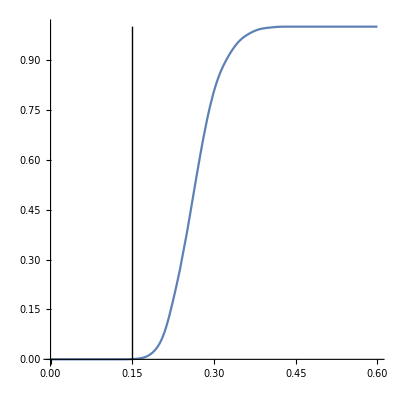

```mathematica
SmoothHistogram[Select[clusteredCancerrandomdata,#<.5&],Automatic,"CDF",AspectRatio->1,Epilog->Line[{{Mean@cancerTratioDist,0},{Mean@cancerTratioDist,1}}],PlotRange->{{0,.6},{0,1}}]
```